```mathematica
f[x0_,v0_,x1_,v1_]:=(x0-x1)/(v1-v0)
```

```mathematica
f[0,3,4,2]
```

4

```mathematica
f[0,2,5,3]
```

-5

```mathematica
8+5+2
```

15

```mathematica
Sum[i/(2^(i+1)),{i,0,n}]
```

2^(-n-1) (-n+2^(n+1)-2)

```mathematica
N[1/4+2/8+3/16+4/32+5/64+6/128]
```

0.9375

```mathematica
p:=0.51
```

0.960784

1

```mathematica
G[p_]:=p*Sum[i*(1-p)^i,{i,0,∞}]
```

```mathematica
B[p_]:=p/(1-p)
```

```mathematica
F[p_]:=G[p]/(B[p]+G[p])
```

```mathematica
F[0.4]
```

0.692308

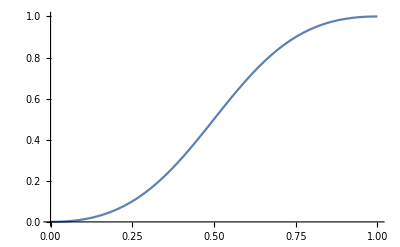

```mathematica
Plot[F[1-x],{x,0,1},ImageSize->Full]
```